```mathematica
NS["det_hessian"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\neurobayes\\";
```

```mathematica
ClearAll[states];states[n_]:=states[n]=Tuples[{0,1},n]
```

```mathematica
states[4];
```

```mathematica
ClearAll[vars];vars[n_]:=vars[n]=aboveanddiag[Table[h[i,j],{i,n},{j,n}]]
```

```mathematica
vars[4];
```

```mathematica
ClearAll[probs];probs[n_]:=probs[n]=Block[{coe=mfromaboveanddiag[vars[n]],tab},
tab=Table[Exp[s.coe.s],{s,states[n]}];
tab/Total[tab]]
```

```mathematica
probs[4];
```

```mathematica
ClearAll[z];z[n_]:=z[n]=Block[{coe=mfromaboveanddiag[vars[n]]},
Sum[Exp[s.coe.s],{s,states[n]}]]
```

```mathematica
z[4];
```

```mathematica
ClearAll[det];det[n_]:=det[n]=
Simplify@Det[Simplify@D[Log[z[n]],{vars[n],2}]]
```

```mathematica
ClearAll[hess];hess[n_]:=hess[n]=Simplify@D[Log[z[n]],{vars[n],2}]
```

```mathematica
hess[4];
```

```mathematica
ndet[n_,vals_]:=Det[hess[n]/.vals]
```

```mathematica
nprodprob[n_,k_,vals_]:=Block[{coe=mfromaboveanddiag[vars[n]],
ntab,colls},
ntab=(probs[n]/.vals);
If[k==0,k=(n^2+n)/2+1];
colls=Subsets[ntab,{k}];
Total[(Times@@#)&/@colls]]
```

```mathematica
rsubs[n_,rang_:10]:=MapThread[Function[{x,y},x->y],
{vars[n],RandomReal[{-rang,rang},(n^2+n)/2]}];
```

```mathematica
rd=rsubs[4];{nprodprob[4,8,rd],ndet[4,rd]}
```

{1.77368×10^-46,4.42768×10^-81}

```mathematica
{nprodprob[4,4,rd],ndet[4,rd]}
```

{1.93956×10^-12,4.42768×10^-81}

```mathematica
rd3=rsubs[3];
```

```mathematica
{nprodprob[3,7,rd],ndet[3,rd]}
```

{5.37841×10^-55,5.37841×10^-55}

```mathematica
rd=rsubs[4];Table[{i,nprodprob[4,i,rd],ndet[3,rd]},{i,16}]//MF
```

(1 | 1. | 7.21955×10^-25
2 | 0.104488 | 7.21955×10^-25
3 | 0.00373148 | 7.21955×10^-25
4 | 0.0000440613 | 7.21955×10^-25
5 | 3.23443×10^-8 | 7.21955×10^-25
6 | 5.91623×10^-12 | 7.21955×10^-25
7 | 1.47144×10^-17 | 7.21955×10^-25
8 | 9.76652×10^-24 | 7.21955×10^-25
9 | 1.88027×10^-30 | 7.21955×10^-25
10 | 1.60445×10^-37 | 7.21955×10^-25
11 | 6.76645×10^-45 | 7.21955×10^-25
12 | 1.36903×10^-52 | 7.21955×10^-25
13 | 1.06459×10^-60 | 7.21955×10^-25
14 | 7.12212×10^-70 | 7.21955×10^-25
15 | 5.81112×10^-83 | 7.21955×10^-25
16 | 1.00943×10^-96 | 7.21955×10^-25)

```mathematica
Subsets[Table[i,{i,5}],{6}]
```

{}

```mathematica
ndet[
```

```mathematica
num[n_,samples_:1]:=Table[Block[{su=rsubs[n],nd,np},
nd=ndet[n,su];np=nprodprob[n,su];
{nd-np,nd/np}],samples]
```

```mathematica
num[2,10]
```

{{2.68389×10^-34,1.},{-4.29178×10^-21,1.},{-4.1876×10^-24,1.},{5.42101×10^-19,1.},{-9.38685×10^-21,1.},{-2.64698×10^-21,1.},{1.79545×10^-19,1.},{9.68743×10^-32,1.},{3.38284×10^-20,1.},{9.08768×10^-28,1.}}

```mathematica
num[3,10]
```

{{1.26903×10^-47,1.},{3.11756×10^-35,1.},{6.85939×10^-30,1.},{9.59835×10^-32,1.},{1.37917×10^-29,1.},{1.5856×10^-40,1.},{1.84889×10^-31,1.},{5.8587×10^-48,1.},{-1.11304×10^-31,1.},{1.02315×10^-34,1.}}

```mathematica
num[4,10]
```

{{-9.03514×10^-41,0.00605203},{-5.38426×10^-55,0.989081},{-1.33526×10^-44,0.255209},{-2.18898×10^-46,0.954526},{-1.31333×10^-50,0.279773},{-9.50713×10^-48,0.0204003},{-3.06207×10^-53,0.493703},{-4.38508×10^-68,0.748177},{-9.70183×10^-76,0.664313},{-1.70874×10^-39,0.210816}}

```mathematica
ndet[4,rsubs[4]]
```

9.88802×10^-62

```mathematica
nprodprob[4,rsubs[4]]
```

2.60842×10^-67

```mathematica
vars[3]
```

vars[3]

```mathematica
Simplify[det[2]*z[2]^4]
```

ⅇ^(2 h[1,1]+h[1,2]+2 h[2,2])

```mathematica
Timing[det[3]]
```

{17.9557,(ⅇ^(3 h[1,1]+h[1,2]+h[1,3]+3 h[2,2]+h[2,3]+3 h[3,3]) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3])+ⅇ^(h[1,2]+h[2,2]+h[2,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3])+ⅇ^(h[1,3]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,3]+h[3,3])+ⅇ^(h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3])))/(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^7}

```mathematica
result=det[4];
```

$Aborted

```mathematica
ClearAll[prodprob];prodprob[n_]:=prodprob[n]=
Block[{coe=mfromaboveanddiag[vars[n]]},
Simplify[Exp@(Sum[s.coe.s,{s,states[n]}])/(z[n]^(2^n))]]
```

```mathematica
prodprob[2]
```

ⅇ^(2 h[1,1]+h[1,2]+2 h[2,2])/((1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2]))^4)

```mathematica
det[2]==prodprob[2]
```

True

```mathematica
det[1]==prodprob[1]
```

True

```mathematica
det[3]
```

(ⅇ^(3 h[1,1]+h[1,2]+h[1,3]+3 h[2,2]+h[2,3]+3 h[3,3]) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3])+ⅇ^(h[1,2]+h[2,2]+h[2,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3])+ⅇ^(h[1,3]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,3]+h[3,3])+ⅇ^(h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3])))/(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^7

```mathematica
prodprob[3]
```

ⅇ^(2 (2 h[1,1]+h[1,2]+h[1,3]+2 h[2,2]+h[2,3]+2 h[3,3]))/(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^8

```mathematica
prodprob[3]*z[3]^8
```

ⅇ^(2 (2 h[1,1]+h[1,2]+h[1,3]+2 h[2,2]+h[2,3]+2 h[3,3]))

```mathematica
z[3]^8
```

(1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3])+ⅇ^(h[1,1]+h[1,2]+h[1,3]+h[2,2]+h[2,3]+h[3,3]))^8

```mathematica
Map[Element[#,Reals]&,vars[2]]
```

{h[1,1]∈ℝ,h[1,2]∈ℝ,h[2,2]∈ℝ}

```mathematica
Assuming[Map[Element[#,Reals]&,vars[3]],FS[det[3]*z[3]^8]]
```

ⅇ^(3 h[1,1]+h[1,2]+h[1,3]+3 h[2,2]+h[2,3]+3 h[3,3]) (1+ⅇ^h[1,1]+ⅇ^h[2,2]+ⅇ^(h[1,1]+h[1,2]+h[2,2])+ⅇ^h[3,3]+ⅇ^(h[1,1]+h[1,3]+h[3,3])+ⅇ^(h[2,2]+h[2,3]+h[3,3]) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3]))) (1+ⅇ^(h[1,1]+h[1,2]+h[1,3])+ⅇ^(h[1,2]+h[2,2]+h[2,3]) (1+ⅇ^(h[1,1]+h[1,3]))+ⅇ^(h[1,3]+h[2,3]+h[3,3]) (1+ⅇ^h[1,2] (ⅇ^h[1,1]+ⅇ^h[2,2] (1+ⅇ^h[1,1]))))

```mathematica
ClearAll[rat];rat[n_]:=rat[n]=Assuming[Map[Element[#,Reals]&,vars[n]],ExpandAll[det[n]*z[n]^(2^n)-prodprob[n]*z[n]^(2^n)]]
```

```mathematica
ClearAll[rtab];rtab[n_,samples_]:=Table[map=MapThread[Function[{x,y},x->y],{vars[n],RandomReal[{-10,10},(n^2+n)/2]}];
Log[(det[n]*z[n]^(2^n))/.map]-Log[(prodprob[n]*z[n]^(2^n))/.map],samples]//N
```

```mathematica
rtab[3,10]
```

{30.9483,15.5912,32.129,13.8611,29.6771,34.0034,15.7961,22.3649,18.0404,9.85598}

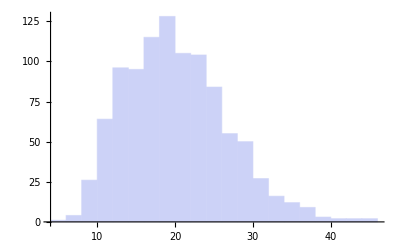

```mathematica
Histogram[rtab[3,1000],"FreedmanDiaconis",PlotRange->All]
```

```mathematica
rtab[4,10]
```

$Aborted

```mathematica
FS[prodprob[3]==det[3]]
```

$Aborted